1.11082 x

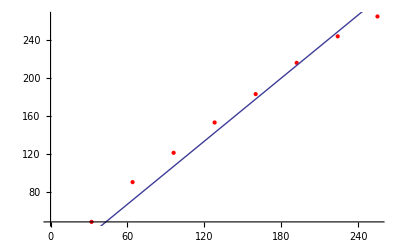

1.06527 x

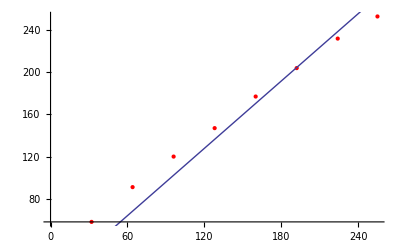

```mathematica
voltages={32,64,96,128,160,192,224,255};
rFreq={{32,48},{64,90},{96,121},{128,153},{160,183},{192,216},{224,244},{255,265}};
lFreq={{32,58},{64,91},{96,120},{128,147},{160,177},{192,204},{224,232},{255,253}};
rf=Fit[rFreq, {x},x];
rf
Show[ListPlot[rFreq,PlotStyle->Red],Plot[rf,{x,0,255}]]
lf=Fit[lFreq, {x},x];
lf
Show[ListPlot[lFreq,PlotStyle->Red],Plot[lf,{x,0,255}]]
```